```mathematica
dataPath=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"data/dataOccupancyPreprocessed.csv"}];
```

```mathematica
data=SemanticImport[dataPath,{"DateTime","Real","Real","Real","Real","Real","Boolean"},"Dataset",HeaderLines->1]
```

Dataset[<>]

```mathematica
trainData=Values@Normal[data[[All,{"Temperature","Humidity","Light","CO2","HumidityRatio"}]]];
```

```mathematica
clusters=ClusteringComponents[trainData,2,1,Method->"KMeans"]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,18443,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}
 |  |  |  |

```mathematica
rules=Map[clusters[[#]]->data[[#,"Occupancy"]]&,Range[Length[data]]];
```

```mathematica
classifier=Classify[rules,Method->"Markov"]
```

ClassifierFunction[…]

```mathematica
cm=ClassifierMeasurements[classifier,rules]
```

ClassifierMeasurementsObject[…]

```mathematica
cm/@{"Accuracy","FScore","ConfusionFunction"}//TableForm
```

0.800414
<|False→0.889144,True→0.|>
<|False→<|False→15091,True→0,Indeterminate→0|>,True→<|False→3763,True→0,Indeterminate→0|>|>

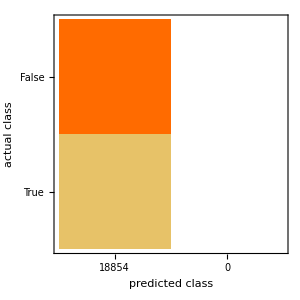

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
15/(15+3)
```

5/6

```mathematica
N[5/6]
```

0.833333

```mathematica
cluster[_method,_clusters]:=
```